# Tour de TNB Appendix: 1.1 Sharpest Curves 1.2 Feed Zones

## Problem Statement

```mathematica
2.1
```

```mathematica
Clear[r]
```

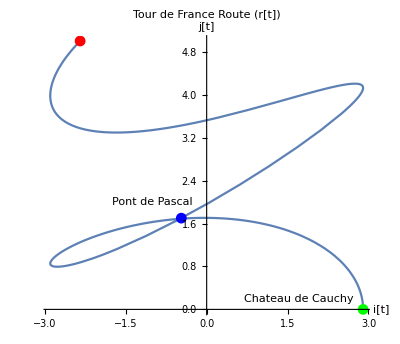

```mathematica
r[t_]={2.9Cos[3.2π*t],(Sin[4π*t]+5t)};
Plot1=ParametricPlot[r[t],{t,0,1},AxesLabel->{Style["i[t]",Medium],Style["j[t]",Medium]},PlotLabel->Style["Tour de France Route (r[t])",FontSize->14]];(*Plot villages, bridge*)
deCauchy = Graphics[{Green,Disk[{2.9,0},.1]}];
text1=Graphics[Text[Style["Chateau de Cauchy",Medium],{1.7,.2}]];
deLaplace = Graphics[{Red,Disk[{2.9Cos[3.2π],(Sin[4π]+5)},.1]}];
text2=Graphics[Text[Style["Chateau de Laplace",Medium],{2.9Cos[3.2π]+1.2,(Sin[4π]+5.12)}]];
PontdePascal = Graphics[{Blue,Disk[{-.47,1.7},.1]}];
text3=Graphics[Text[Style["Pont de Pascal",Medium],{-1,2}]];
Show[{Plot1,deCauchy,deLaplace,PontdePascal,text1,text2,text3}]
```

```mathematica
2.2
```

{-29.154 Sin[10.0531 t],5+4 π Cos[4 π t]}

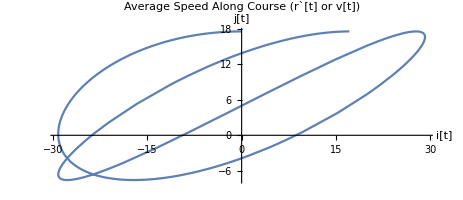

```mathematica
Subscript[Speed, 1]=D[r[t],t]
MagSpeed=Norm[Subscript[Speed, 1]];
ParametricPlot[Subscript[Speed, 1],{t,0,1},AxesLabel->{Style["i[t]",Small],Style["j[t]",Small]},PlotLabel->Style["Average Speed Along Course (r`[t] or v[t])",FontSize->14]]
avgspeed = NIntegrate[MagSpeed,{t,0,1}];
```

## 2.3

```mathematica
∑_(t=0)^1 MagSpeed
r[1]-r[0]
```

42.1067

{-5.24615,5}

## 2.4

```mathematica
f[t_?NumericQ]:=NIntegrate[Norm[r[t]],{t,0,1}];
FindRoot[f[t]==1,{t,1.2}]
```

FindRoot[f[t]==1,{t,1.2}]

## 2.5(a)

```mathematica
Acc=r''[t];
```

```mathematica
normal=Cross[{-29.15397982531328 Sin[10.053096491487338 t],5+4 π Cos[4 π t]},{-293.0877722947496 Cos[10.053096491487338 t],-16 π^2 Sin[4 π t]}];
mag2=Norm[normal];
```

```mathematica
k=Simplify[ArcCurvature[r[t],t]];
```

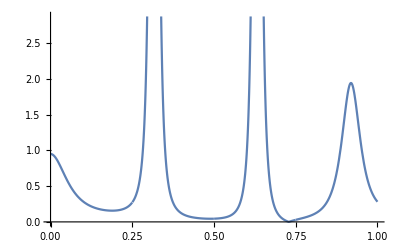

```mathematica
Plot[k,{t,0,1}]
```

```mathematica
(*use given code*)
(*acceleration is r``[t]*)
(*normal to accleration is
```